# The Mobile 3rd Space

## Declare Base Constants

## Declare Thermal Resistances

## Equations

```mathematica
eqn={Ttile'[t]==(Q-(Ttile[t]-Tair[t])/Rair)/Ctile,(Ttile[t]-Tair[t])/Rair==(Tair[t]-Tout)/U+(Tair[t]-Tout)/Rwindow,Tair[0]==21}
```

{Ttile'[t]==(Q-(-Tair[t]+Ttile[t])/Rair)/Ctile,(-Tair[t]+Ttile[t])/Rair==(-Tout+Tair[t])/Rwindow+(-Tout+Tair[t])/U,Tair[0]==21}

```mathematica
sol=DSolveValue[eqn,{Ttile[t],Tair[t]},t];
airTemp=sol⟦2⟧
```

1/(Rwindow+U)ⅇ^(-(t (Rwindow+U))/(Ctile (Rair Rwindow+Rair U+Rwindow U))) (21 Rwindow-Rwindow Tout+ⅇ^((t (Rwindow+U))/(Ctile (Rair Rwindow+Rair U+Rwindow U))) Rwindow Tout+21 U-Q Rwindow U+ⅇ^((t (Rwindow+U))/(Ctile (Rair Rwindow+Rair U+Rwindow U))) Q Rwindow U-Tout U+ⅇ^((t (Rwindow+U))/(Ctile (Rair Rwindow+Rair U+Rwindow U))) Tout U)

```mathematica
eqn2={C1 Ttile'[t]==Q-(Ttile[t]-Twall[t])/Subscript[R, eff],C2 Twall'[t]==(Ttile[t]-Twall[t])/Subscript[R, eff]-(Twall[t]-Tout)/R4,Tair[t]==Twall[t]+((Ttile[t]-Twall[t]) (R2+R3))/Subscript[R, eff],Tair[0]==20,Ttile[0]==100,Twall[0]==50} (* + 3 is from -Tout @ Tout=-3*)
```

{C1 Ttile'[t]==Q-(Ttile[t]-Twall[t])/R_eff,C2 Twall'[t]==(Ttile[t]-Twall[t])/R_eff-(-Tout+Twall[t])/R4,Tair[t]==((R2+R3) (Ttile[t]-Twall[t]))/R_eff+Twall[t],Tair[0]==20,Ttile[0]==100,Twall[0]==50}

```mathematica
sol=DSolveValue[eqn2,{Ttile[t],Twall[t],Tair[t]},t];
airTemp=sol⟦2⟧
```

DSolveValue::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{Ttile[t],Twall[t],Tair[t]}

```mathematica
airTemp=sol⟦3⟧
```

(((C2 R4+C1 C2 R1 R4) ((C1 C2 (1+1+1+C1 R3) R4^2)/(1)^2+1/1^2))/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)+(C1 (R2+3+1) (1/1^2+1))/(1+C1 R1+5+C1 C2 R2 R4+C1 C2 R3 R4)) (1)+(1+1) 1
 |  |  |  |

0.321499 (82.1749-568.094 (0.916025 2.71828^(-0.0265603 t)+0.0839749 2.71828^(-0.00430385 t))+4. (-0.27735 2.71828^(-0.0265603 t)+0.27735 2.71828^(-0.00430385 t)))+0.660424 (264.347-568.094 (-0.27735 2.71828^(-0.0265603 t)+0.27735 2.71828^(-0.00430385 t))+4. (0.0839749 2.71828^(-0.0265603 t)+0.916025 2.71828^(-0.00430385 t)))

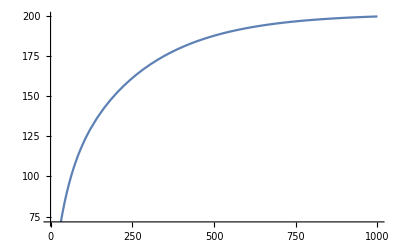

```mathematica
airTemp/.{R1->6,R2->6,R3->6,R4->6,C1->9,C2->9,C3->9,Q->10,Tout->21,C[1]->4};
N[%]
Plot[%,{t,0,1000}]
```

```mathematica
airTemp
```

(((C2 R4+C1 C2 R1 R4) ((C1 C2 (1+C1 R1+C1 R2+C1 R3) R4^2)/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)^2+(C1^2 R4 (R1+R2+R3+R4+C2 R1 R4+C2 R2 R4+C2 R3 R4))/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)^2))/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)+(C1 (R2+R3+R4+C2 R2 R4+C2 R3 R4) ((C1 C2 R4^2)/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)^2+(C1^2 (R1+R2+R3+R4+C2 R1 R4+C2 R2 R4+C2 R3 R4)^2)/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)^2))/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)) (-((ⅇ^(((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) (C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2+C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^3+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2+3 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R2+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2+3 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2^2+C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^3+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3+3 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R3+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3+6 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R3+3 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R3+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2+3 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3^2+3 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3^2+C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^3+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4+2 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R4-2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R4+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4+4 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R4-4 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R4+2 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R4-2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R4+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4+4 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3 R4-4 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3 R4+4 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3 R4-4 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3 R4+2 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2 R4-2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2 R4+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^2+2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^2+C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^2+C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^2+2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^2+C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^2+C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^2+2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^2+C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^2+C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) (C1 C2 Q R4^2+C2^2 Q R4^2+2 C1 C2^2 Q R1 R4^2+C1^2 C2^2 Q R1^2 R4^2+2 C1 C2^2 Q R2 R4^2+2 C1^2 C2^2 Q R1 R2 R4^2+C1^2 C2^2 Q R2^2 R4^2+2 C1 C2^2 Q R3 R4^2+2 C1^2 C2^2 Q R1 R3 R4^2+2 C1^2 C2^2 Q R2 R3 R4^2+C1^2 C2^2 Q R3^2 R4^2-C1^2 R1 Tout-C1^2 R2 Tout-C1^2 R3 Tout-C1^2 R4 Tout-C1 C2 R4 Tout-2 C1^2 C2 R1 R4 Tout-2 C1^2 C2 R2 R4 Tout-2 C1^2 C2 R3 R4 Tout))/(C1^3 C2 (R1+R2+R3)^2 R4 (C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2) (-C1 R1-C1 R2-C1 R3-C1 R4-C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2))))+(ⅇ^(((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) (C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2+C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^3+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2+3 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R2+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2+3 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2^2+C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^3+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3+3 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R3+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3+6 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R3+3 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R3+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2+3 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3^2+3 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3^2+C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^3+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4+2 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R4-2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R4+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4+4 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R4-4 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R4+2 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R4-2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R4+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4+4 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3 R4-4 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3 R4+4 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3 R4-4 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3 R4+2 C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2 R4-2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2 R4+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^2+2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^2+C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^2+C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^2+2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^2+C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^2+C1^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^2+2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^2+C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^2-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) (C1 C2 Q R4^2+C2^2 Q R4^2+2 C1 C2^2 Q R1 R4^2+C1^2 C2^2 Q R1^2 R4^2+2 C1 C2^2 Q R2 R4^2+2 C1^2 C2^2 Q R1 R2 R4^2+C1^2 C2^2 Q R2^2 R4^2+2 C1 C2^2 Q R3 R4^2+2 C1^2 C2^2 Q R1 R3 R4^2+2 C1^2 C2^2 Q R2 R3 R4^2+C1^2 C2^2 Q R3^2 R4^2-C1^2 R1 Tout-C1^2 R2 Tout-C1^2 R3 Tout-C1^2 R4 Tout-C1 C2 R4 Tout-2 C1^2 C2 R1 R4 Tout-2 C1^2 C2 R2 R4 Tout-2 C1^2 C2 R3 R4 Tout))/(C1^3 C2 (R1+R2+R3)^2 R4 (C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2) (C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)))+(ⅇ^(((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) (C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) (-C1 C2 Q R1 R4^2-C1 C2 Q R2 R4^2-C1 C2 Q R3 R4^2-C1 C2 Q R4^3-C2^2 Q R4^3-2 C1 C2^2 Q R1 R4^3-2 C1 C2^2 Q R2 R4^3-2 C1 C2^2 Q R3 R4^3+C1^2 R1^2 Tout+2 C1^2 R1 R2 Tout+C1^2 R2^2 Tout+2 C1^2 R1 R3 Tout+2 C1^2 R2 R3 Tout+C1^2 R3^2 Tout+2 C1^2 R1 R4 Tout+2 C1^2 C2 R1^2 R4 Tout+2 C1^2 R2 R4 Tout+4 C1^2 C2 R1 R2 R4 Tout+2 C1^2 C2 R2^2 R4 Tout+2 C1^2 R3 R4 Tout+4 C1^2 C2 R1 R3 R4 Tout+4 C1^2 C2 R2 R3 R4 Tout+2 C1^2 C2 R3^2 R4 Tout+C1^2 R4^2 Tout+C1 C2 R4^2 Tout+2 C1^2 C2 R1 R4^2 Tout+C1^2 C2^2 R1^2 R4^2 Tout+2 C1^2 C2 R2 R4^2 Tout+2 C1^2 C2^2 R1 R2 R4^2 Tout+C1^2 C2^2 R2^2 R4^2 Tout+2 C1^2 C2 R3 R4^2 Tout+2 C1^2 C2^2 R1 R3 R4^2 Tout+2 C1^2 C2^2 R2 R3 R4^2 Tout+C1^2 C2^2 R3^2 R4^2 Tout))/(C1^2 C2^2 (R1+R2+R3)^2 R4^2 (C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2) (-C1 R1-C1 R2-C1 R3-C1 R4-C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)))-(ⅇ^(((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) (C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) (-C1 C2 Q R1 R4^2-C1 C2 Q R2 R4^2-C1 C2 Q R3 R4^2-C1 C2 Q R4^3-C2^2 Q R4^3-2 C1 C2^2 Q R1 R4^3-2 C1 C2^2 Q R2 R4^3-2 C1 C2^2 Q R3 R4^3+C1^2 R1^2 Tout+2 C1^2 R1 R2 Tout+C1^2 R2^2 Tout+2 C1^2 R1 R3 Tout+2 C1^2 R2 R3 Tout+C1^2 R3^2 Tout+2 C1^2 R1 R4 Tout+2 C1^2 C2 R1^2 R4 Tout+2 C1^2 R2 R4 Tout+4 C1^2 C2 R1 R2 R4 Tout+2 C1^2 C2 R2^2 R4 Tout+2 C1^2 R3 R4 Tout+4 C1^2 C2 R1 R3 R4 Tout+4 C1^2 C2 R2 R3 R4 Tout+2 C1^2 C2 R3^2 R4 Tout+C1^2 R4^2 Tout+C1 C2 R4^2 Tout+2 C1^2 C2 R1 R4^2 Tout+C1^2 C2^2 R1^2 R4^2 Tout+2 C1^2 C2 R2 R4^2 Tout+2 C1^2 C2^2 R1 R2 R4^2 Tout+C1^2 C2^2 R2^2 R4^2 Tout+2 C1^2 C2 R3 R4^2 Tout+2 C1^2 C2^2 R1 R3 R4^2 Tout+2 C1^2 C2^2 R2 R3 R4^2 Tout+C1^2 C2^2 R3^2 R4^2 Tout))/(C1^2 C2^2 (R1+R2+R3)^2 R4^2 (C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2) (C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)))+(-((ⅇ^(((-C1 R1-C1 R2-C1 R3-C1 R4-C2 R4-√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4))) t)/(2 C1 C2 (R1+R2+R3) R4)) (-C2 R4+1/2 (C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)))))/(√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4))))+(ⅇ^(((-C1 R1-C1 R2-C1 R3-C1 R4-C2 R4+√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4))) t)/(2 C1 C2 (R1+R2+R3) R4)) (-C2 R4+1/2 (C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)))))/(√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)))) C[1]+((-(C2 ⅇ^(((-C1 R1-C1 R2-C1 R3-C1 R4-C2 R4-√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4))) t)/(2 C1 C2 (R1+R2+R3) R4)) R4)/(√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)))+(C2 ⅇ^(((-C1 R1-C1 R2-C1 R3-C1 R4-C2 R4+√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4))) t)/(2 C1 C2 (R1+R2+R3) R4)) R4)/(√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)))) (21+63 C1 R1+63 C1^2 R1^2+21 C1^3 R1^3+63 C1 R2-Q R2+126 C1^2 R1 R2-3 C1 Q R1 R2+63 C1^3 R1^2 R2-3 C1^2 Q R1^2 R2-C1^3 Q R1^3 R2+63 C1^2 R2^2-3 C1 Q R2^2+63 C1^3 R1 R2^2-6 C1^2 Q R1 R2^2-3 C1^3 Q R1^2 R2^2+21 C1^3 R2^3-3 C1^2 Q R2^3-3 C1^3 Q R1 R2^3-C1^3 Q R2^4+63 C1 R3-Q R3+126 C1^2 R1 R3-3 C1 Q R1 R3+63 C1^3 R1^2 R3-3 C1^2 Q R1^2 R3-C1^3 Q R1^3 R3+126 C1^2 R2 R3-6 C1 Q R2 R3+126 C1^3 R1 R2 R3-12 C1^2 Q R1 R2 R3-6 C1^3 Q R1^2 R2 R3+63 C1^3 R2^2 R3-9 C1^2 Q R2^2 R3-9 C1^3 Q R1 R2^2 R3-4 C1^3 Q R2^3 R3+63 C1^2 R3^2-3 C1 Q R3^2+63 C1^3 R1 R3^2-6 C1^2 Q R1 R3^2-3 C1^3 Q R1^2 R3^2+63 C1^3 R2 R3^2-9 C1^2 Q R2 R3^2-9 C1^3 Q R1 R2 R3^2-6 C1^3 Q R2^2 R3^2+21 C1^3 R3^3-3 C1^2 Q R3^3-3 C1^3 Q R1 R3^3-4 C1^3 Q R2 R3^3-C1^3 Q R3^4+63 C1 R4+63 C2 R4-Q R4+126 C1^2 R1 R4+189 C1 C2 R1 R4-3 C1 Q R1 R4+63 C1^3 R1^2 R4+189 C1^2 C2 R1^2 R4-3 C1^2 Q R1^2 R4+63 C1^3 C2 R1^3 R4-C1^3 Q R1^3 R4+126 C1^2 R2 R4+189 C1 C2 R2 R4-6 C1 Q R2 R4-3 C2 Q R2 R4+126 C1^3 R1 R2 R4+378 C1^2 C2 R1 R2 R4-12 C1^2 Q R1 R2 R4-9 C1 C2 Q R1 R2 R4+189 C1^3 C2 R1^2 R2 R4-6 C1^3 Q R1^2 R2 R4-9 C1^2 C2 Q R1^2 R2 R4-3 C1^3 C2 Q R1^3 R2 R4+63 C1^3 R2^2 R4+189 C1^2 C2 R2^2 R4-9 C1^2 Q R2^2 R4-9 C1 C2 Q R2^2 R4+189 C1^3 C2 R1 R2^2 R4-9 C1^3 Q R1 R2^2 R4-18 C1^2 C2 Q R1 R2^2 R4-9 C1^3 C2 Q R1^2 R2^2 R4+63 C1^3 C2 R2^3 R4-4 C1^3 Q R2^3 R4-9 C1^2 C2 Q R2^3 R4-9 C1^3 C2 Q R1 R2^3 R4-3 C1^3 C2 Q R2^4 R4+126 C1^2 R3 R4+189 C1 C2 R3 R4-6 C1 Q R3 R4-3 C2 Q R3 R4+126 C1^3 R1 R3 R4+378 C1^2 C2 R1 R3 R4-12 C1^2 Q R1 R3 R4-9 C1 C2 Q R1 R3 R4+189 C1^3 C2 R1^2 R3 R4-6 C1^3 Q R1^2 R3 R4-9 C1^2 C2 Q R1^2 R3 R4-3 C1^3 C2 Q R1^3 R3 R4+126 C1^3 R2 R3 R4+378 C1^2 C2 R2 R3 R4-18 C1^2 Q R2 R3 R4-18 C1 C2 Q R2 R3 R4+378 C1^3 C2 R1 R2 R3 R4-18 C1^3 Q R1 R2 R3 R4-36 C1^2 C2 Q R1 R2 R3 R4-18 C1^3 C2 Q R1^2 R2 R3 R4+189 C1^3 C2 R2^2 R3 R4-12 C1^3 Q R2^2 R3 R4-27 C1^2 C2 Q R2^2 R3 R4-27 C1^3 C2 Q R1 R2^2 R3 R4-12 C1^3 C2 Q R2^3 R3 R4+63 C1^3 R3^2 R4+189 C1^2 C2 R3^2 R4-9 C1^2 Q R3^2 R4-9 C1 C2 Q R3^2 R4+189 C1^3 C2 R1 R3^2 R4-9 C1^3 Q R1 R3^2 R4-18 C1^2 C2 Q R1 R3^2 R4-9 C1^3 C2 Q R1^2 R3^2 R4+189 C1^3 C2 R2 R3^2 R4-12 C1^3 Q R2 R3^2 R4-27 C1^2 C2 Q R2 R3^2 R4-27 C1^3 C2 Q R1 R2 R3^2 R4-18 C1^3 C2 Q R2^2 R3^2 R4+63 C1^3 C2 R3^3 R4-4 C1^3 Q R3^3 R4-9 C1^2 C2 Q R3^3 R4-9 C1^3 C2 Q R1 R3^3 R4-12 C1^3 C2 Q R2 R3^3 R4-3 C1^3 C2 Q R3^4 R4+63 C1^2 R4^2+126 C1 C2 R4^2+63 C2^2 R4^2-3 C1 Q R4^2-3 C2 Q R4^2+63 C1^3 R1 R4^2+252 C1^2 C2 R1 R4^2+189 C1 C2^2 R1 R4^2-6 C1^2 Q R1 R4^2-9 C1 C2 Q R1 R4^2+126 C1^3 C2 R1^2 R4^2+189 C1^2 C2^2 R1^2 R4^2-3 C1^3 Q R1^2 R4^2-9 C1^2 C2 Q R1^2 R4^2+63 C1^3 C2^2 R1^3 R4^2-3 C1^3 C2 Q R1^3 R4^2+63 C1^3 R2 R4^2+252 C1^2 C2 R2 R4^2+189 C1 C2^2 R2 R4^2-9 C1^2 Q R2 R4^2-15 C1 C2 Q R2 R4^2-3 C2^2 Q R2 R4^2+252 C1^3 C2 R1 R2 R4^2+378 C1^2 C2^2 R1 R2 R4^2-9 C1^3 Q R1 R2 R4^2-30 C1^2 C2 Q R1 R2 R4^2-9 C1 C2^2 Q R1 R2 R4^2+189 C1^3 C2^2 R1^2 R2 R4^2-15 C1^3 C2 Q R1^2 R2 R4^2-9 C1^2 C2^2 Q R1^2 R2 R4^2-3 C1^3 C2^2 Q R1^3 R2 R4^2+126 C1^3 C2 R2^2 R4^2+189 C1^2 C2^2 R2^2 R4^2-6 C1^3 Q R2^2 R4^2-21 C1^2 C2 Q R2^2 R4^2-9 C1 C2^2 Q R2^2 R4^2+189 C1^3 C2^2 R1 R2^2 R4^2-21 C1^3 C2 Q R1 R2^2 R4^2-18 C1^2 C2^2 Q R1 R2^2 R4^2-9 C1^3 C2^2 Q R1^2 R2^2 R4^2+63 C1^3 C2^2 R2^3 R4^2-9 C1^3 C2 Q R2^3 R4^2-9 C1^2 C2^2 Q R2^3 R4^2-9 C1^3 C2^2 Q R1 R2^3 R4^2-3 C1^3 C2^2 Q R2^4 R4^2+63 C1^3 R3 R4^2+252 C1^2 C2 R3 R4^2+189 C1 C2^2 R3 R4^2-9 C1^2 Q R3 R4^2-15 C1 C2 Q R3 R4^2-3 C2^2 Q R3 R4^2+252 C1^3 C2 R1 R3 R4^2+378 C1^2 C2^2 R1 R3 R4^2-9 C1^3 Q R1 R3 R4^2-30 C1^2 C2 Q R1 R3 R4^2-9 C1 C2^2 Q R1 R3 R4^2+189 C1^3 C2^2 R1^2 R3 R4^2-15 C1^3 C2 Q R1^2 R3 R4^2-9 C1^2 C2^2 Q R1^2 R3 R4^2-3 C1^3 C2^2 Q R1^3 R3 R4^2+252 C1^3 C2 R2 R3 R4^2+378 C1^2 C2^2 R2 R3 R4^2-12 C1^3 Q R2 R3 R4^2-42 C1^2 C2 Q R2 R3 R4^2-18 C1 C2^2 Q R2 R3 R4^2+378 C1^3 C2^2 R1 R2 R3 R4^2-42 C1^3 C2 Q R1 R2 R3 R4^2-36 C1^2 C2^2 Q R1 R2 R3 R4^2-18 C1^3 C2^2 Q R1^2 R2 R3 R4^2+189 C1^3 C2^2 R2^2 R3 R4^2-27 C1^3 C2 Q R2^2 R3 R4^2-27 C1^2 C2^2 Q R2^2 R3 R4^2-27 C1^3 C2^2 Q R1 R2^2 R3 R4^2-12 C1^3 C2^2 Q R2^3 R3 R4^2+126 C1^3 C2 R3^2 R4^2+189 C1^2 C2^2 R3^2 R4^2-6 C1^3 Q R3^2 R4^2-21 C1^2 C2 Q R3^2 R4^2-9 C1 C2^2 Q R3^2 R4^2+189 C1^3 C2^2 R1 R3^2 R4^2-21 C1^3 C2 Q R1 R3^2 R4^2-18 C1^2 C2^2 Q R1 R3^2 R4^2-9 C1^3 C2^2 Q R1^2 R3^2 R4^2+189 C1^3 C2^2 R2 R3^2 R4^2-27 C1^3 C2 Q R2 R3^2 R4^2-27 C1^2 C2^2 Q R2 R3^2 R4^2-27 C1^3 C2^2 Q R1 R2 R3^2 R4^2-18 C1^3 C2^2 Q R2^2 R3^2 R4^2+63 C1^3 C2^2 R3^3 R4^2-9 C1^3 C2 Q R3^3 R4^2-9 C1^2 C2^2 Q R3^3 R4^2-9 C1^3 C2^2 Q R1 R3^3 R4^2-12 C1^3 C2^2 Q R2 R3^3 R4^2-3 C1^3 C2^2 Q R3^4 R4^2+21 C1^3 R4^3+63 C1^2 C2 R4^3+63 C1 C2^2 R4^3+21 C2^3 R4^3-3 C1^2 Q R4^3-6 C1 C2 Q R4^3-3 C2^2 Q R4^3+63 C1^3 C2 R1 R4^3+126 C1^2 C2^2 R1 R4^3+63 C1 C2^3 R1 R4^3-3 C1^3 Q R1 R4^3-12 C1^2 C2 Q R1 R4^3-9 C1 C2^2 Q R1 R4^3+63 C1^3 C2^2 R1^2 R4^3+63 C1^2 C2^3 R1^2 R4^3-6 C1^3 C2 Q R1^2 R4^3-9 C1^2 C2^2 Q R1^2 R4^3+21 C1^3 C2^3 R1^3 R4^3-3 C1^3 C2^2 Q R1^3 R4^3+63 C1^3 C2 R2 R4^3+126 C1^2 C2^2 R2 R4^3+63 C1 C2^3 R2 R4^3-4 C1^3 Q R2 R4^3-15 C1^2 C2 Q R2 R4^3-12 C1 C2^2 Q R2 R4^3-C2^3 Q R2 R4^3+126 C1^3 C2^2 R1 R2 R4^3+126 C1^2 C2^3 R1 R2 R4^3-15 C1^3 C2 Q R1 R2 R4^3-24 C1^2 C2^2 Q R1 R2 R4^3-3 C1 C2^3 Q R1 R2 R4^3+63 C1^3 C2^3 R1^2 R2 R4^3-12 C1^3 C2^2 Q R1^2 R2 R4^3-3 C1^2 C2^3 Q R1^2 R2 R4^3-C1^3 C2^3 Q R1^3 R2 R4^3+63 C1^3 C2^2 R2^2 R4^3+63 C1^2 C2^3 R2^2 R4^3-9 C1^3 C2 Q R2^2 R4^3-15 C1^2 C2^2 Q R2^2 R4^3-3 C1 C2^3 Q R2^2 R4^3+63 C1^3 C2^3 R1 R2^2 R4^3-15 C1^3 C2^2 Q R1 R2^2 R4^3-6 C1^2 C2^3 Q R1 R2^2 R4^3-3 C1^3 C2^3 Q R1^2 R2^2 R4^3+21 C1^3 C2^3 R2^3 R4^3-6 C1^3 C2^2 Q R2^3 R4^3-3 C1^2 C2^3 Q R2^3 R4^3-3 C1^3 C2^3 Q R1 R2^3 R4^3-C1^3 C2^3 Q R2^4 R4^3+63 C1^3 C2 R3 R4^3+126 C1^2 C2^2 R3 R4^3+63 C1 C2^3 R3 R4^3-4 C1^3 Q R3 R4^3-15 C1^2 C2 Q R3 R4^3-12 C1 C2^2 Q R3 R4^3-C2^3 Q R3 R4^3+126 C1^3 C2^2 R1 R3 R4^3+126 C1^2 C2^3 R1 R3 R4^3-15 C1^3 C2 Q R1 R3 R4^3-24 C1^2 C2^2 Q R1 R3 R4^3-3 C1 C2^3 Q R1 R3 R4^3+63 C1^3 C2^3 R1^2 R3 R4^3-12 C1^3 C2^2 Q R1^2 R3 R4^3-3 C1^2 C2^3 Q R1^2 R3 R4^3-C1^3 C2^3 Q R1^3 R3 R4^3+126 C1^3 C2^2 R2 R3 R4^3+126 C1^2 C2^3 R2 R3 R4^3-18 C1^3 C2 Q R2 R3 R4^3-30 C1^2 C2^2 Q R2 R3 R4^3-6 C1 C2^3 Q R2 R3 R4^3+126 C1^3 C2^3 R1 R2 R3 R4^3-30 C1^3 C2^2 Q R1 R2 R3 R4^3-12 C1^2 C2^3 Q R1 R2 R3 R4^3-6 C1^3 C2^3 Q R1^2 R2 R3 R4^3+63 C1^3 C2^3 R2^2 R3 R4^3-18 C1^3 C2^2 Q R2^2 R3 R4^3-9 C1^2 C2^3 Q R2^2 R3 R4^3-9 C1^3 C2^3 Q R1 R2^2 R3 R4^3-4 C1^3 C2^3 Q R2^3 R3 R4^3+63 C1^3 C2^2 R3^2 R4^3+63 C1^2 C2^3 R3^2 R4^3-9 C1^3 C2 Q R3^2 R4^3-15 C1^2 C2^2 Q R3^2 R4^3-3 C1 C2^3 Q R3^2 R4^3+63 C1^3 C2^3 R1 R3^2 R4^3-15 C1^3 C2^2 Q R1 R3^2 R4^3-6 C1^2 C2^3 Q R1 R3^2 R4^3-3 C1^3 C2^3 Q R1^2 R3^2 R4^3+63 C1^3 C2^3 R2 R3^2 R4^3-18 C1^3 C2^2 Q R2 R3^2 R4^3-9 C1^2 C2^3 Q R2 R3^2 R4^3-9 C1^3 C2^3 Q R1 R2 R3^2 R4^3-6 C1^3 C2^3 Q R2^2 R3^2 R4^3+21 C1^3 C2^3 R3^3 R4^3-6 C1^3 C2^2 Q R3^3 R4^3-3 C1^2 C2^3 Q R3^3 R4^3-3 C1^3 C2^3 Q R1 R3^3 R4^3-4 C1^3 C2^3 Q R2 R3^3 R4^3-C1^3 C2^3 Q R3^4 R4^3-C1^3 Q R4^4-3 C1^2 C2 Q R4^4-3 C1 C2^2 Q R4^4-C2^3 Q R4^4-3 C1^3 C2 Q R1 R4^4-6 C1^2 C2^2 Q R1 R4^4-3 C1 C2^3 Q R1 R4^4-3 C1^3 C2^2 Q R1^2 R4^4-3 C1^2 C2^3 Q R1^2 R4^4-C1^3 C2^3 Q R1^3 R4^4-3 C1^3 C2 Q R2 R4^4-6 C1^2 C2^2 Q R2 R4^4-3 C1 C2^3 Q R2 R4^4-6 C1^3 C2^2 Q R1 R2 R4^4-6 C1^2 C2^3 Q R1 R2 R4^4-3 C1^3 C2^3 Q R1^2 R2 R4^4-3 C1^3 C2^2 Q R2^2 R4^4-3 C1^2 C2^3 Q R2^2 R4^4-3 C1^3 C2^3 Q R1 R2^2 R4^4-C1^3 C2^3 Q R2^3 R4^4-3 C1^3 C2 Q R3 R4^4-6 C1^2 C2^2 Q R3 R4^4-3 C1 C2^3 Q R3 R4^4-6 C1^3 C2^2 Q R1 R3 R4^4-6 C1^2 C2^3 Q R1 R3 R4^4-3 C1^3 C2^3 Q R1^2 R3 R4^4-6 C1^3 C2^2 Q R2 R3 R4^4-6 C1^2 C2^3 Q R2 R3 R4^4-6 C1^3 C2^3 Q R1 R2 R3 R4^4-3 C1^3 C2^3 Q R2^2 R3 R4^4-3 C1^3 C2^2 Q R3^2 R4^4-3 C1^2 C2^3 Q R3^2 R4^4-3 C1^3 C2^3 Q R1 R3^2 R4^4-3 C1^3 C2^3 Q R2 R3^2 R4^4-C1^3 C2^3 Q R3^3 R4^4-Tout-3 C1 R1 Tout-3 C1^2 R1^2 Tout-C1^3 R1^3 Tout-3 C1 R2 Tout-6 C1^2 R1 R2 Tout-3 C1^3 R1^2 R2 Tout-3 C1^2 R2^2 Tout-3 C1^3 R1 R2^2 Tout-C1^3 R2^3 Tout-3 C1 R3 Tout-6 C1^2 R1 R3 Tout-3 C1^3 R1^2 R3 Tout-6 C1^2 R2 R3 Tout-6 C1^3 R1 R2 R3 Tout-3 C1^3 R2^2 R3 Tout-3 C1^2 R3^2 Tout-3 C1^3 R1 R3^2 Tout-3 C1^3 R2 R3^2 Tout-C1^3 R3^3 Tout-3 C1 R4 Tout-3 C2 R4 Tout-6 C1^2 R1 R4 Tout-9 C1 C2 R1 R4 Tout-3 C1^3 R1^2 R4 Tout-9 C1^2 C2 R1^2 R4 Tout-3 C1^3 C2 R1^3 R4 Tout-6 C1^2 R2 R4 Tout-9 C1 C2 R2 R4 Tout-6 C1^3 R1 R2 R4 Tout-18 C1^2 C2 R1 R2 R4 Tout-9 C1^3 C2 R1^2 R2 R4 Tout-3 C1^3 R2^2 R4 Tout-9 C1^2 C2 R2^2 R4 Tout-9 C1^3 C2 R1 R2^2 R4 Tout-3 C1^3 C2 R2^3 R4 Tout-6 C1^2 R3 R4 Tout-9 C1 C2 R3 R4 Tout-6 C1^3 R1 R3 R4 Tout-18 C1^2 C2 R1 R3 R4 Tout-9 C1^3 C2 R1^2 R3 R4 Tout-6 C1^3 R2 R3 R4 Tout-18 C1^2 C2 R2 R3 R4 Tout-18 C1^3 C2 R1 R2 R3 R4 Tout-9 C1^3 C2 R2^2 R3 R4 Tout-3 C1^3 R3^2 R4 Tout-9 C1^2 C2 R3^2 R4 Tout-9 C1^3 C2 R1 R3^2 R4 Tout-9 C1^3 C2 R2 R3^2 R4 Tout-3 C1^3 C2 R3^3 R4 Tout-3 C1^2 R4^2 Tout-6 C1 C2 R4^2 Tout-3 C2^2 R4^2 Tout-3 C1^3 R1 R4^2 Tout-12 C1^2 C2 R1 R4^2 Tout-9 C1 C2^2 R1 R4^2 Tout-6 C1^3 C2 R1^2 R4^2 Tout-9 C1^2 C2^2 R1^2 R4^2 Tout-3 C1^3 C2^2 R1^3 R4^2 Tout-3 C1^3 R2 R4^2 Tout-12 C1^2 C2 R2 R4^2 Tout-9 C1 C2^2 R2 R4^2 Tout-12 C1^3 C2 R1 R2 R4^2 Tout-18 C1^2 C2^2 R1 R2 R4^2 Tout-9 C1^3 C2^2 R1^2 R2 R4^2 Tout-6 C1^3 C2 R2^2 R4^2 Tout-9 C1^2 C2^2 R2^2 R4^2 Tout-9 C1^3 C2^2 R1 R2^2 R4^2 Tout-3 C1^3 C2^2 R2^3 R4^2 Tout-3 C1^3 R3 R4^2 Tout-12 C1^2 C2 R3 R4^2 Tout-9 C1 C2^2 R3 R4^2 Tout-12 C1^3 C2 R1 R3 R4^2 Tout-18 C1^2 C2^2 R1 R3 R4^2 Tout-9 C1^3 C2^2 R1^2 R3 R4^2 Tout-12 C1^3 C2 R2 R3 R4^2 Tout-18 C1^2 C2^2 R2 R3 R4^2 Tout-18 C1^3 C2^2 R1 R2 R3 R4^2 Tout-9 C1^3 C2^2 R2^2 R3 R4^2 Tout-6 C1^3 C2 R3^2 R4^2 Tout-9 C1^2 C2^2 R3^2 R4^2 Tout-9 C1^3 C2^2 R1 R3^2 R4^2 Tout-9 C1^3 C2^2 R2 R3^2 R4^2 Tout-3 C1^3 C2^2 R3^3 R4^2 Tout-C1^3 R4^3 Tout-3 C1^2 C2 R4^3 Tout-3 C1 C2^2 R4^3 Tout-C2^3 R4^3 Tout-3 C1^3 C2 R1 R4^3 Tout-6 C1^2 C2^2 R1 R4^3 Tout-3 C1 C2^3 R1 R4^3 Tout-3 C1^3 C2^2 R1^2 R4^3 Tout-3 C1^2 C2^3 R1^2 R4^3 Tout-C1^3 C2^3 R1^3 R4^3 Tout-3 C1^3 C2 R2 R4^3 Tout-6 C1^2 C2^2 R2 R4^3 Tout-3 C1 C2^3 R2 R4^3 Tout-6 C1^3 C2^2 R1 R2 R4^3 Tout-6 C1^2 C2^3 R1 R2 R4^3 Tout-3 C1^3 C2^3 R1^2 R2 R4^3 Tout-3 C1^3 C2^2 R2^2 R4^3 Tout-3 C1^2 C2^3 R2^2 R4^3 Tout-3 C1^3 C2^3 R1 R2^2 R4^3 Tout-C1^3 C2^3 R2^3 R4^3 Tout-3 C1^3 C2 R3 R4^3 Tout-6 C1^2 C2^2 R3 R4^3 Tout-3 C1 C2^3 R3 R4^3 Tout-6 C1^3 C2^2 R1 R3 R4^3 Tout-6 C1^2 C2^3 R1 R3 R4^3 Tout-3 C1^3 C2^3 R1^2 R3 R4^3 Tout-6 C1^3 C2^2 R2 R3 R4^3 Tout-6 C1^2 C2^3 R2 R3 R4^3 Tout-6 C1^3 C2^3 R1 R2 R3 R4^3 Tout-3 C1^3 C2^3 R2^2 R3 R4^3 Tout-3 C1^3 C2^2 R3^2 R4^3 Tout-3 C1^2 C2^3 R3^2 R4^3 Tout-3 C1^3 C2^3 R1 R3^2 R4^3 Tout-3 C1^3 C2^3 R2 R3^2 R4^3 Tout-C1^3 C2^3 R3^3 R4^3 Tout-C1^3 R1^2 R2 C[1]-2 C1^3 R1 R2^2 C[1]-C1^3 R2^3 C[1]-C1^3 R1^2 R3 C[1]-4 C1^3 R1 R2 R3 C[1]-3 C1^3 R2^2 R3 C[1]-2 C1^3 R1 R3^2 C[1]-3 C1^3 R2 R3^2 C[1]-C1^3 R3^3 C[1]-C1^3 R1^2 R4 C[1]-4 C1^3 R1 R2 R4 C[1]-3 C1^3 C2 R1^2 R2 R4 C[1]-3 C1^3 R2^2 R4 C[1]-6 C1^3 C2 R1 R2^2 R4 C[1]-3 C1^3 C2 R2^3 R4 C[1]-4 C1^3 R1 R3 R4 C[1]-3 C1^3 C2 R1^2 R3 R4 C[1]-6 C1^3 R2 R3 R4 C[1]-12 C1^3 C2 R1 R2 R3 R4 C[1]-9 C1^3 C2 R2^2 R3 R4 C[1]-3 C1^3 R3^2 R4 C[1]-6 C1^3 C2 R1 R3^2 R4 C[1]-9 C1^3 C2 R2 R3^2 R4 C[1]-3 C1^3 C2 R3^3 R4 C[1]-2 C1^3 R1 R4^2 C[1]-C1^2 C2 R1 R4^2 C[1]-3 C1^3 C2 R1^2 R4^2 C[1]-3 C1^3 R2 R4^2 C[1]-2 C1^2 C2 R2 R4^2 C[1]-9 C1^3 C2 R1 R2 R4^2 C[1]-3 C1^3 C2^2 R1^2 R2 R4^2 C[1]-6 C1^3 C2 R2^2 R4^2 C[1]-6 C1^3 C2^2 R1 R2^2 R4^2 C[1]-3 C1^3 C2^2 R2^3 R4^2 C[1]-3 C1^3 R3 R4^2 C[1]-2 C1^2 C2 R3 R4^2 C[1]-9 C1^3 C2 R1 R3 R4^2 C[1]-3 C1^3 C2^2 R1^2 R3 R4^2 C[1]-12 C1^3 C2 R2 R3 R4^2 C[1]-12 C1^3 C2^2 R1 R2 R3 R4^2 C[1]-9 C1^3 C2^2 R2^2 R3 R4^2 C[1]-6 C1^3 C2 R3^2 R4^2 C[1]-6 C1^3 C2^2 R1 R3^2 R4^2 C[1]-9 C1^3 C2^2 R2 R3^2 R4^2 C[1]-3 C1^3 C2^2 R3^3 R4^2 C[1]-C1^3 R4^3 C[1]-2 C1^2 C2 R4^3 C[1]-C1 C2^2 R4^3 C[1]-3 C1^3 C2 R1 R4^3 C[1]-3 C1^2 C2^2 R1 R4^3 C[1]-3 C1^3 C2^2 R1^2 R4^3 C[1]-3 C1^3 C2 R2 R4^3 C[1]-3 C1^2 C2^2 R2 R4^3 C[1]-6 C1^3 C2^2 R1 R2 R4^3 C[1]-C1^3 C2^3 R1^2 R2 R4^3 C[1]-3 C1^3 C2^2 R2^2 R4^3 C[1]-2 C1^3 C2^3 R1 R2^2 R4^3 C[1]-C1^3 C2^3 R2^3 R4^3 C[1]-3 C1^3 C2 R3 R4^3 C[1]-3 C1^2 C2^2 R3 R4^3 C[1]-6 C1^3 C2^2 R1 R3 R4^3 C[1]-C1^3 C2^3 R1^2 R3 R4^3 C[1]-6 C1^3 C2^2 R2 R3 R4^3 C[1]-4 C1^3 C2^3 R1 R2 R3 R4^3 C[1]-3 C1^3 C2^3 R2^2 R3 R4^3 C[1]-3 C1^3 C2^2 R3^2 R4^3 C[1]-2 C1^3 C2^3 R1 R3^2 R4^3 C[1]-3 C1^3 C2^3 R2 R3^2 R4^3 C[1]-C1^3 C2^3 R3^3 R4^3 C[1]))/(C2 R4 (C1^2 R1 R2+C1^2 R2^2+C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+C1^2 R1 R4+2 C1^2 R2 R4+C1 C2 R2 R4+3 C1^2 C2 R1 R2 R4+3 C1^2 C2 R2^2 R4+2 C1^2 R3 R4+C1 C2 R3 R4+3 C1^2 C2 R1 R3 R4+6 C1^2 C2 R2 R3 R4+3 C1^2 C2 R3^2 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2+3 C1^2 C2 R1 R4^2+3 C1 C2^2 R1 R4^2+3 C1^2 C2^2 R1^2 R4^2+C1^3 C2^2 R1^3 R4^2+3 C1^2 C2 R2 R4^2+3 C1 C2^2 R2 R4^2+6 C1^2 C2^2 R1 R2 R4^2+2 C1^3 C2^2 R1^2 R2 R4^2+3 C1^2 C2^2 R2^2 R4^2+C1^3 C2^2 R1 R2^2 R4^2+3 C1^2 C2 R3 R4^2+3 C1 C2^2 R3 R4^2+6 C1^2 C2^2 R1 R3 R4^2+2 C1^3 C2^2 R1^2 R3 R4^2+6 C1^2 C2^2 R2 R3 R4^2+2 C1^3 C2^2 R1 R2 R3 R4^2+3 C1^2 C2^2 R3^2 R4^2+C1^3 C2^2 R1 R3^2 R4^2)))+(((C2 R4+C1 C2 R1 R4) ((C1 C2 R4^2)/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)^2+(C2^2 (1+C1 R1+C1 R2+C1 R3)^2 R4^2)/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)^2))/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)+(C1 (R2+R3+R4+C2 R2 R4+C2 R3 R4) ((C2^2 (1+C1 R1+C1 R2+C1 R3) R4^2)/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)^2+(C1 C2 R4 (R1+R2+R3+R4+C2 R1 R4+C2 R2 R4+C2 R3 R4))/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)^2))/(1+C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)) ((ⅇ^(((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) (C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) (C1 C2 Q R4^2+C2^2 Q R4^2+2 C1 C2^2 Q R1 R4^2+C1^2 C2^2 Q R1^2 R4^2+2 C1 C2^2 Q R2 R4^2+2 C1^2 C2^2 Q R1 R2 R4^2+C1^2 C2^2 Q R2^2 R4^2+2 C1 C2^2 Q R3 R4^2+2 C1^2 C2^2 Q R1 R3 R4^2+2 C1^2 C2^2 Q R2 R3 R4^2+C1^2 C2^2 Q R3^2 R4^2-C1^2 R1 Tout-C1^2 R2 Tout-C1^2 R3 Tout-C1^2 R4 Tout-C1 C2 R4 Tout-2 C1^2 C2 R1 R4 Tout-2 C1^2 C2 R2 R4 Tout-2 C1^2 C2 R3 R4 Tout))/(C1^2 C2^2 (R1+R2+R3)^2 R4 (C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2) (-C1 R1-C1 R2-C1 R3-C1 R4-C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)))-(ⅇ^(((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) (C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4+2 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2+C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) (C1 C2 Q R4^2+C2^2 Q R4^2+2 C1 C2^2 Q R1 R4^2+C1^2 C2^2 Q R1^2 R4^2+2 C1 C2^2 Q R2 R4^2+2 C1^2 C2^2 Q R1 R2 R4^2+C1^2 C2^2 Q R2^2 R4^2+2 C1 C2^2 Q R3 R4^2+2 C1^2 C2^2 Q R1 R3 R4^2+2 C1^2 C2^2 Q R2 R3 R4^2+C1^2 C2^2 Q R3^2 R4^2-C1^2 R1 Tout-C1^2 R2 Tout-C1^2 R3 Tout-C1^2 R4 Tout-C1 C2 R4 Tout-2 C1^2 C2 R1 R4 Tout-2 C1^2 C2 R2 R4 Tout-2 C1^2 C2 R3 R4 Tout))/(C1^2 C2^2 (R1+R2+R3)^2 R4 (C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2) (C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)))+((C1^2 R1^3+3 C1^2 R1^2 R2+3 C1^2 R1 R2^2+C1^2 R2^3+3 C1^2 R1^2 R3+6 C1^2 R1 R2 R3+3 C1^2 R2^2 R3+3 C1^2 R1 R3^2+3 C1^2 R2 R3^2+C1^2 R3^3+3 C1^2 R1^2 R4-2 C1 C2 R1^2 R4+C1^2 C2 R1^3 R4+6 C1^2 R1 R2 R4-4 C1 C2 R1 R2 R4+3 C1^2 C2 R1^2 R2 R4+3 C1^2 R2^2 R4-2 C1 C2 R2^2 R4+3 C1^2 C2 R1 R2^2 R4+C1^2 C2 R2^3 R4+6 C1^2 R1 R3 R4-4 C1 C2 R1 R3 R4+3 C1^2 C2 R1^2 R3 R4+6 C1^2 R2 R3 R4-4 C1 C2 R2 R3 R4+6 C1^2 C2 R1 R2 R3 R4+3 C1^2 C2 R2^2 R3 R4+3 C1^2 R3^2 R4-2 C1 C2 R3^2 R4+3 C1^2 C2 R1 R3^2 R4+3 C1^2 C2 R2 R3^2 R4+C1^2 C2 R3^3 R4+3 C1^2 R1 R4^2+C2^2 R1 R4^2+2 C1^2 C2 R1^2 R4^2-2 C1 C2^2 R1^2 R4^2+3 C1^2 R2 R4^2+C2^2 R2 R4^2+4 C1^2 C2 R1 R2 R4^2-4 C1 C2^2 R1 R2 R4^2+2 C1^2 C2 R2^2 R4^2-2 C1 C2^2 R2^2 R4^2+3 C1^2 R3 R4^2+C2^2 R3 R4^2+4 C1^2 C2 R1 R3 R4^2-4 C1 C2^2 R1 R3 R4^2+4 C1^2 C2 R2 R3 R4^2-4 C1 C2^2 R2 R3 R4^2+2 C1^2 C2 R3^2 R4^2-2 C1 C2^2 R3^2 R4^2+C1^2 R4^3+2 C1 C2 R4^3+C2^2 R4^3+C1^2 C2 R1 R4^3+2 C1 C2^2 R1 R4^3+C2^3 R1 R4^3+C1^2 C2 R2 R4^3+2 C1 C2^2 R2 R4^3+C2^3 R2 R4^3+C1^2 C2 R3 R4^3+2 C1 C2^2 R3 R4^3+C2^3 R3 R4^3+C1 R1^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 R1 R2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 R2^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 R1 R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 R2 R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 R3^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 R1 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C2 R1 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 C2 R1^2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C2 R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 C2 R1 R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 C2 R2^2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C2 R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 C2 R1 R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+2 C1 C2 R2 R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 C2 R3^2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C2 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 C2 R1 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C2^2 R1 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 C2 R2 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C2^2 R2 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C1 C2 R3 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C2^2 R3 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) (-C1 C2 Q R1 R4^2-C1 C2 Q R2 R4^2-C1 C2 Q R3 R4^2-C1 C2 Q R4^3-C2^2 Q R4^3-2 C1 C2^2 Q R1 R4^3-2 C1 C2^2 Q R2 R4^3-2 C1 C2^2 Q R3 R4^3+C1^2 R1^2 Tout+2 C1^2 R1 R2 Tout+C1^2 R2^2 Tout+2 C1^2 R1 R3 Tout+2 C1^2 R2 R3 Tout+C1^2 R3^2 Tout+2 C1^2 R1 R4 Tout+2 C1^2 C2 R1^2 R4 Tout+2 C1^2 R2 R4 Tout+4 C1^2 C2 R1 R2 R4 Tout+2 C1^2 C2 R2^2 R4 Tout+2 C1^2 R3 R4 Tout+4 C1^2 C2 R1 R3 R4 Tout+4 C1^2 C2 R2 R3 R4 Tout+2 C1^2 C2 R3^2 R4 Tout+C1^2 R4^2 Tout+C1 C2 R4^2 Tout+2 C1^2 C2 R1 R4^2 Tout+C1^2 C2^2 R1^2 R4^2 Tout+2 C1^2 C2 R2 R4^2 Tout+2 C1^2 C2^2 R1 R2 R4^2 Tout+C1^2 C2^2 R2^2 R4^2 Tout+2 C1^2 C2 R3 R4^2 Tout+2 C1^2 C2^2 R1 R3 R4^2 Tout+2 C1^2 C2^2 R2 R3 R4^2 Tout+C1^2 C2^2 R3^2 R4^2 Tout))/(C1 C2^3 (R1+R2+R3)^2 R4^3 (C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2) (C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)))-(ⅇ^(((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) (C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^3+3 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R2+3 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2^2+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^3+3 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R3+6 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R3+3 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R3+3 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3^2+3 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3^2+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^3+3 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R4+C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^3 R4+6 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R4-4 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R4+3 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R2 R4+3 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R4+3 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2^2 R4+C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^3 R4+6 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3 R4-4 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3 R4+3 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R3 R4+6 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3 R4-4 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3 R4+6 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R3 R4+3 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R3 R4+3 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2 R4-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2 R4+3 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3^2 R4+3 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3^2 R4+C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^3 R4+3 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^2+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^2+2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R4^2-2 C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R4^2+3 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^2+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^2+4 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R4^2-4 C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R4^2+2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R4^2-2 C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R4^2+3 C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^2+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^2+4 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3 R4^2-4 C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3 R4^2+4 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3 R4^2-4 C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3 R4^2+2 C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2 R4^2-2 C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2 R4^2+C1^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^3+2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^3+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^3+C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^3+2 C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^3+C2^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^3+C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^3+2 C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^3+C2^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^3+C1^2 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^3+2 C1 C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^3+C2^3 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^3-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1^2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2^2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-2 C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R3 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3^2 R4 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R1 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R2 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)-C1 C2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)+C2^2 ⅇ^(-((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) t)/(2 C1 C2 (R1+R2+R3) R4)) R3 R4^2 √(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)) (-C1 C2 Q R1 R4^2-C1 C2 Q R2 R4^2-C1 C2 Q R3 R4^2-C1 C2 Q R4^3-C2^2 Q R4^3-2 C1 C2^2 Q R1 R4^3-2 C1 C2^2 Q R2 R4^3-2 C1 C2^2 Q R3 R4^3+C1^2 R1^2 Tout+2 C1^2 R1 R2 Tout+C1^2 R2^2 Tout+2 C1^2 R1 R3 Tout+2 C1^2 R2 R3 Tout+C1^2 R3^2 Tout+2 C1^2 R1 R4 Tout+2 C1^2 C2 R1^2 R4 Tout+2 C1^2 R2 R4 Tout+4 C1^2 C2 R1 R2 R4 Tout+2 C1^2 C2 R2^2 R4 Tout+2 C1^2 R3 R4 Tout+4 C1^2 C2 R1 R3 R4 Tout+4 C1^2 C2 R2 R3 R4 Tout+2 C1^2 C2 R3^2 R4 Tout+C1^2 R4^2 Tout+C1 C2 R4^2 Tout+2 C1^2 C2 R1 R4^2 Tout+C1^2 C2^2 R1^2 R4^2 Tout+2 C1^2 C2 R2 R4^2 Tout+2 C1^2 C2^2 R1 R2 R4^2 Tout+C1^2 C2^2 R2^2 R4^2 Tout+2 C1^2 C2 R3 R4^2 Tout+2 C1^2 C2^2 R1 R3 R4^2 Tout+2 C1^2 C2^2 R2 R3 R4^2 Tout+C1^2 C2^2 R3^2 R4^2 Tout))/(C1 C2^3 (R1+R2+R3)^2 R4^3 (C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2) (-C1 R1-C1 R2-C1 R3-C1 R4-C2 R4+√(C1^2 R1^2+2 C1^2 R1 R2+C1^2 R2^2+2 C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+2 C1^2 R1 R4-2 C1 C2 R1 R4+2 C1^2 R2 R4-2 C1 C2 R2 R4+2 C1^2 R3 R4-2 C1 C2 R3 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2)))+(-(C1 ⅇ^(((-C1 R1-C1 R2-C1 R3-C1 R4-C2 R4-√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4))) t)/(2 C1 C2 (R1+R2+R3) R4)) R4)/(√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)))+(C1 ⅇ^(((-C1 R1-C1 R2-C1 R3-C1 R4-C2 R4+√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4))) t)/(2 C1 C2 (R1+R2+R3) R4)) R4)/(√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)))) C[1]+((-((ⅇ^(((-C1 R1-C1 R2-C1 R3-C1 R4-C2 R4-√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4))) t)/(2 C1 C2 (R1+R2+R3) R4)) (-C1 (R1+R2+R3+R4)+1/2 (C1 R1+C1 R2+C1 R3+C1 R4+C2 R4-√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)))))/(√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4))))+(ⅇ^(((-C1 R1-C1 R2-C1 R3-C1 R4-C2 R4+√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4))) t)/(2 C1 C2 (R1+R2+R3) R4)) (-C1 (R1+R2+R3+R4)+1/2 (C1 R1+C1 R2+C1 R3+C1 R4+C2 R4+√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)))))/(√((C1 R1+C1 R2+C1 R3+C1 R4+C2 R4)^2-4 (C1 C2 R1 R4+C1 C2 R2 R4+C1 C2 R3 R4)))) (21+63 C1 R1+63 C1^2 R1^2+21 C1^3 R1^3+63 C1 R2-Q R2+126 C1^2 R1 R2-3 C1 Q R1 R2+63 C1^3 R1^2 R2-3 C1^2 Q R1^2 R2-C1^3 Q R1^3 R2+63 C1^2 R2^2-3 C1 Q R2^2+63 C1^3 R1 R2^2-6 C1^2 Q R1 R2^2-3 C1^3 Q R1^2 R2^2+21 C1^3 R2^3-3 C1^2 Q R2^3-3 C1^3 Q R1 R2^3-C1^3 Q R2^4+63 C1 R3-Q R3+126 C1^2 R1 R3-3 C1 Q R1 R3+63 C1^3 R1^2 R3-3 C1^2 Q R1^2 R3-C1^3 Q R1^3 R3+126 C1^2 R2 R3-6 C1 Q R2 R3+126 C1^3 R1 R2 R3-12 C1^2 Q R1 R2 R3-6 C1^3 Q R1^2 R2 R3+63 C1^3 R2^2 R3-9 C1^2 Q R2^2 R3-9 C1^3 Q R1 R2^2 R3-4 C1^3 Q R2^3 R3+63 C1^2 R3^2-3 C1 Q R3^2+63 C1^3 R1 R3^2-6 C1^2 Q R1 R3^2-3 C1^3 Q R1^2 R3^2+63 C1^3 R2 R3^2-9 C1^2 Q R2 R3^2-9 C1^3 Q R1 R2 R3^2-6 C1^3 Q R2^2 R3^2+21 C1^3 R3^3-3 C1^2 Q R3^3-3 C1^3 Q R1 R3^3-4 C1^3 Q R2 R3^3-C1^3 Q R3^4+63 C1 R4+63 C2 R4-Q R4+126 C1^2 R1 R4+189 C1 C2 R1 R4-3 C1 Q R1 R4+63 C1^3 R1^2 R4+189 C1^2 C2 R1^2 R4-3 C1^2 Q R1^2 R4+63 C1^3 C2 R1^3 R4-C1^3 Q R1^3 R4+126 C1^2 R2 R4+189 C1 C2 R2 R4-6 C1 Q R2 R4-3 C2 Q R2 R4+126 C1^3 R1 R2 R4+378 C1^2 C2 R1 R2 R4-12 C1^2 Q R1 R2 R4-9 C1 C2 Q R1 R2 R4+189 C1^3 C2 R1^2 R2 R4-6 C1^3 Q R1^2 R2 R4-9 C1^2 C2 Q R1^2 R2 R4-3 C1^3 C2 Q R1^3 R2 R4+63 C1^3 R2^2 R4+189 C1^2 C2 R2^2 R4-9 C1^2 Q R2^2 R4-9 C1 C2 Q R2^2 R4+189 C1^3 C2 R1 R2^2 R4-9 C1^3 Q R1 R2^2 R4-18 C1^2 C2 Q R1 R2^2 R4-9 C1^3 C2 Q R1^2 R2^2 R4+63 C1^3 C2 R2^3 R4-4 C1^3 Q R2^3 R4-9 C1^2 C2 Q R2^3 R4-9 C1^3 C2 Q R1 R2^3 R4-3 C1^3 C2 Q R2^4 R4+126 C1^2 R3 R4+189 C1 C2 R3 R4-6 C1 Q R3 R4-3 C2 Q R3 R4+126 C1^3 R1 R3 R4+378 C1^2 C2 R1 R3 R4-12 C1^2 Q R1 R3 R4-9 C1 C2 Q R1 R3 R4+189 C1^3 C2 R1^2 R3 R4-6 C1^3 Q R1^2 R3 R4-9 C1^2 C2 Q R1^2 R3 R4-3 C1^3 C2 Q R1^3 R3 R4+126 C1^3 R2 R3 R4+378 C1^2 C2 R2 R3 R4-18 C1^2 Q R2 R3 R4-18 C1 C2 Q R2 R3 R4+378 C1^3 C2 R1 R2 R3 R4-18 C1^3 Q R1 R2 R3 R4-36 C1^2 C2 Q R1 R2 R3 R4-18 C1^3 C2 Q R1^2 R2 R3 R4+189 C1^3 C2 R2^2 R3 R4-12 C1^3 Q R2^2 R3 R4-27 C1^2 C2 Q R2^2 R3 R4-27 C1^3 C2 Q R1 R2^2 R3 R4-12 C1^3 C2 Q R2^3 R3 R4+63 C1^3 R3^2 R4+189 C1^2 C2 R3^2 R4-9 C1^2 Q R3^2 R4-9 C1 C2 Q R3^2 R4+189 C1^3 C2 R1 R3^2 R4-9 C1^3 Q R1 R3^2 R4-18 C1^2 C2 Q R1 R3^2 R4-9 C1^3 C2 Q R1^2 R3^2 R4+189 C1^3 C2 R2 R3^2 R4-12 C1^3 Q R2 R3^2 R4-27 C1^2 C2 Q R2 R3^2 R4-27 C1^3 C2 Q R1 R2 R3^2 R4-18 C1^3 C2 Q R2^2 R3^2 R4+63 C1^3 C2 R3^3 R4-4 C1^3 Q R3^3 R4-9 C1^2 C2 Q R3^3 R4-9 C1^3 C2 Q R1 R3^3 R4-12 C1^3 C2 Q R2 R3^3 R4-3 C1^3 C2 Q R3^4 R4+63 C1^2 R4^2+126 C1 C2 R4^2+63 C2^2 R4^2-3 C1 Q R4^2-3 C2 Q R4^2+63 C1^3 R1 R4^2+252 C1^2 C2 R1 R4^2+189 C1 C2^2 R1 R4^2-6 C1^2 Q R1 R4^2-9 C1 C2 Q R1 R4^2+126 C1^3 C2 R1^2 R4^2+189 C1^2 C2^2 R1^2 R4^2-3 C1^3 Q R1^2 R4^2-9 C1^2 C2 Q R1^2 R4^2+63 C1^3 C2^2 R1^3 R4^2-3 C1^3 C2 Q R1^3 R4^2+63 C1^3 R2 R4^2+252 C1^2 C2 R2 R4^2+189 C1 C2^2 R2 R4^2-9 C1^2 Q R2 R4^2-15 C1 C2 Q R2 R4^2-3 C2^2 Q R2 R4^2+252 C1^3 C2 R1 R2 R4^2+378 C1^2 C2^2 R1 R2 R4^2-9 C1^3 Q R1 R2 R4^2-30 C1^2 C2 Q R1 R2 R4^2-9 C1 C2^2 Q R1 R2 R4^2+189 C1^3 C2^2 R1^2 R2 R4^2-15 C1^3 C2 Q R1^2 R2 R4^2-9 C1^2 C2^2 Q R1^2 R2 R4^2-3 C1^3 C2^2 Q R1^3 R2 R4^2+126 C1^3 C2 R2^2 R4^2+189 C1^2 C2^2 R2^2 R4^2-6 C1^3 Q R2^2 R4^2-21 C1^2 C2 Q R2^2 R4^2-9 C1 C2^2 Q R2^2 R4^2+189 C1^3 C2^2 R1 R2^2 R4^2-21 C1^3 C2 Q R1 R2^2 R4^2-18 C1^2 C2^2 Q R1 R2^2 R4^2-9 C1^3 C2^2 Q R1^2 R2^2 R4^2+63 C1^3 C2^2 R2^3 R4^2-9 C1^3 C2 Q R2^3 R4^2-9 C1^2 C2^2 Q R2^3 R4^2-9 C1^3 C2^2 Q R1 R2^3 R4^2-3 C1^3 C2^2 Q R2^4 R4^2+63 C1^3 R3 R4^2+252 C1^2 C2 R3 R4^2+189 C1 C2^2 R3 R4^2-9 C1^2 Q R3 R4^2-15 C1 C2 Q R3 R4^2-3 C2^2 Q R3 R4^2+252 C1^3 C2 R1 R3 R4^2+378 C1^2 C2^2 R1 R3 R4^2-9 C1^3 Q R1 R3 R4^2-30 C1^2 C2 Q R1 R3 R4^2-9 C1 C2^2 Q R1 R3 R4^2+189 C1^3 C2^2 R1^2 R3 R4^2-15 C1^3 C2 Q R1^2 R3 R4^2-9 C1^2 C2^2 Q R1^2 R3 R4^2-3 C1^3 C2^2 Q R1^3 R3 R4^2+252 C1^3 C2 R2 R3 R4^2+378 C1^2 C2^2 R2 R3 R4^2-12 C1^3 Q R2 R3 R4^2-42 C1^2 C2 Q R2 R3 R4^2-18 C1 C2^2 Q R2 R3 R4^2+378 C1^3 C2^2 R1 R2 R3 R4^2-42 C1^3 C2 Q R1 R2 R3 R4^2-36 C1^2 C2^2 Q R1 R2 R3 R4^2-18 C1^3 C2^2 Q R1^2 R2 R3 R4^2+189 C1^3 C2^2 R2^2 R3 R4^2-27 C1^3 C2 Q R2^2 R3 R4^2-27 C1^2 C2^2 Q R2^2 R3 R4^2-27 C1^3 C2^2 Q R1 R2^2 R3 R4^2-12 C1^3 C2^2 Q R2^3 R3 R4^2+126 C1^3 C2 R3^2 R4^2+189 C1^2 C2^2 R3^2 R4^2-6 C1^3 Q R3^2 R4^2-21 C1^2 C2 Q R3^2 R4^2-9 C1 C2^2 Q R3^2 R4^2+189 C1^3 C2^2 R1 R3^2 R4^2-21 C1^3 C2 Q R1 R3^2 R4^2-18 C1^2 C2^2 Q R1 R3^2 R4^2-9 C1^3 C2^2 Q R1^2 R3^2 R4^2+189 C1^3 C2^2 R2 R3^2 R4^2-27 C1^3 C2 Q R2 R3^2 R4^2-27 C1^2 C2^2 Q R2 R3^2 R4^2-27 C1^3 C2^2 Q R1 R2 R3^2 R4^2-18 C1^3 C2^2 Q R2^2 R3^2 R4^2+63 C1^3 C2^2 R3^3 R4^2-9 C1^3 C2 Q R3^3 R4^2-9 C1^2 C2^2 Q R3^3 R4^2-9 C1^3 C2^2 Q R1 R3^3 R4^2-12 C1^3 C2^2 Q R2 R3^3 R4^2-3 C1^3 C2^2 Q R3^4 R4^2+21 C1^3 R4^3+63 C1^2 C2 R4^3+63 C1 C2^2 R4^3+21 C2^3 R4^3-3 C1^2 Q R4^3-6 C1 C2 Q R4^3-3 C2^2 Q R4^3+63 C1^3 C2 R1 R4^3+126 C1^2 C2^2 R1 R4^3+63 C1 C2^3 R1 R4^3-3 C1^3 Q R1 R4^3-12 C1^2 C2 Q R1 R4^3-9 C1 C2^2 Q R1 R4^3+63 C1^3 C2^2 R1^2 R4^3+63 C1^2 C2^3 R1^2 R4^3-6 C1^3 C2 Q R1^2 R4^3-9 C1^2 C2^2 Q R1^2 R4^3+21 C1^3 C2^3 R1^3 R4^3-3 C1^3 C2^2 Q R1^3 R4^3+63 C1^3 C2 R2 R4^3+126 C1^2 C2^2 R2 R4^3+63 C1 C2^3 R2 R4^3-4 C1^3 Q R2 R4^3-15 C1^2 C2 Q R2 R4^3-12 C1 C2^2 Q R2 R4^3-C2^3 Q R2 R4^3+126 C1^3 C2^2 R1 R2 R4^3+126 C1^2 C2^3 R1 R2 R4^3-15 C1^3 C2 Q R1 R2 R4^3-24 C1^2 C2^2 Q R1 R2 R4^3-3 C1 C2^3 Q R1 R2 R4^3+63 C1^3 C2^3 R1^2 R2 R4^3-12 C1^3 C2^2 Q R1^2 R2 R4^3-3 C1^2 C2^3 Q R1^2 R2 R4^3-C1^3 C2^3 Q R1^3 R2 R4^3+63 C1^3 C2^2 R2^2 R4^3+63 C1^2 C2^3 R2^2 R4^3-9 C1^3 C2 Q R2^2 R4^3-15 C1^2 C2^2 Q R2^2 R4^3-3 C1 C2^3 Q R2^2 R4^3+63 C1^3 C2^3 R1 R2^2 R4^3-15 C1^3 C2^2 Q R1 R2^2 R4^3-6 C1^2 C2^3 Q R1 R2^2 R4^3-3 C1^3 C2^3 Q R1^2 R2^2 R4^3+21 C1^3 C2^3 R2^3 R4^3-6 C1^3 C2^2 Q R2^3 R4^3-3 C1^2 C2^3 Q R2^3 R4^3-3 C1^3 C2^3 Q R1 R2^3 R4^3-C1^3 C2^3 Q R2^4 R4^3+63 C1^3 C2 R3 R4^3+126 C1^2 C2^2 R3 R4^3+63 C1 C2^3 R3 R4^3-4 C1^3 Q R3 R4^3-15 C1^2 C2 Q R3 R4^3-12 C1 C2^2 Q R3 R4^3-C2^3 Q R3 R4^3+126 C1^3 C2^2 R1 R3 R4^3+126 C1^2 C2^3 R1 R3 R4^3-15 C1^3 C2 Q R1 R3 R4^3-24 C1^2 C2^2 Q R1 R3 R4^3-3 C1 C2^3 Q R1 R3 R4^3+63 C1^3 C2^3 R1^2 R3 R4^3-12 C1^3 C2^2 Q R1^2 R3 R4^3-3 C1^2 C2^3 Q R1^2 R3 R4^3-C1^3 C2^3 Q R1^3 R3 R4^3+126 C1^3 C2^2 R2 R3 R4^3+126 C1^2 C2^3 R2 R3 R4^3-18 C1^3 C2 Q R2 R3 R4^3-30 C1^2 C2^2 Q R2 R3 R4^3-6 C1 C2^3 Q R2 R3 R4^3+126 C1^3 C2^3 R1 R2 R3 R4^3-30 C1^3 C2^2 Q R1 R2 R3 R4^3-12 C1^2 C2^3 Q R1 R2 R3 R4^3-6 C1^3 C2^3 Q R1^2 R2 R3 R4^3+63 C1^3 C2^3 R2^2 R3 R4^3-18 C1^3 C2^2 Q R2^2 R3 R4^3-9 C1^2 C2^3 Q R2^2 R3 R4^3-9 C1^3 C2^3 Q R1 R2^2 R3 R4^3-4 C1^3 C2^3 Q R2^3 R3 R4^3+63 C1^3 C2^2 R3^2 R4^3+63 C1^2 C2^3 R3^2 R4^3-9 C1^3 C2 Q R3^2 R4^3-15 C1^2 C2^2 Q R3^2 R4^3-3 C1 C2^3 Q R3^2 R4^3+63 C1^3 C2^3 R1 R3^2 R4^3-15 C1^3 C2^2 Q R1 R3^2 R4^3-6 C1^2 C2^3 Q R1 R3^2 R4^3-3 C1^3 C2^3 Q R1^2 R3^2 R4^3+63 C1^3 C2^3 R2 R3^2 R4^3-18 C1^3 C2^2 Q R2 R3^2 R4^3-9 C1^2 C2^3 Q R2 R3^2 R4^3-9 C1^3 C2^3 Q R1 R2 R3^2 R4^3-6 C1^3 C2^3 Q R2^2 R3^2 R4^3+21 C1^3 C2^3 R3^3 R4^3-6 C1^3 C2^2 Q R3^3 R4^3-3 C1^2 C2^3 Q R3^3 R4^3-3 C1^3 C2^3 Q R1 R3^3 R4^3-4 C1^3 C2^3 Q R2 R3^3 R4^3-C1^3 C2^3 Q R3^4 R4^3-C1^3 Q R4^4-3 C1^2 C2 Q R4^4-3 C1 C2^2 Q R4^4-C2^3 Q R4^4-3 C1^3 C2 Q R1 R4^4-6 C1^2 C2^2 Q R1 R4^4-3 C1 C2^3 Q R1 R4^4-3 C1^3 C2^2 Q R1^2 R4^4-3 C1^2 C2^3 Q R1^2 R4^4-C1^3 C2^3 Q R1^3 R4^4-3 C1^3 C2 Q R2 R4^4-6 C1^2 C2^2 Q R2 R4^4-3 C1 C2^3 Q R2 R4^4-6 C1^3 C2^2 Q R1 R2 R4^4-6 C1^2 C2^3 Q R1 R2 R4^4-3 C1^3 C2^3 Q R1^2 R2 R4^4-3 C1^3 C2^2 Q R2^2 R4^4-3 C1^2 C2^3 Q R2^2 R4^4-3 C1^3 C2^3 Q R1 R2^2 R4^4-C1^3 C2^3 Q R2^3 R4^4-3 C1^3 C2 Q R3 R4^4-6 C1^2 C2^2 Q R3 R4^4-3 C1 C2^3 Q R3 R4^4-6 C1^3 C2^2 Q R1 R3 R4^4-6 C1^2 C2^3 Q R1 R3 R4^4-3 C1^3 C2^3 Q R1^2 R3 R4^4-6 C1^3 C2^2 Q R2 R3 R4^4-6 C1^2 C2^3 Q R2 R3 R4^4-6 C1^3 C2^3 Q R1 R2 R3 R4^4-3 C1^3 C2^3 Q R2^2 R3 R4^4-3 C1^3 C2^2 Q R3^2 R4^4-3 C1^2 C2^3 Q R3^2 R4^4-3 C1^3 C2^3 Q R1 R3^2 R4^4-3 C1^3 C2^3 Q R2 R3^2 R4^4-C1^3 C2^3 Q R3^3 R4^4-Tout-3 C1 R1 Tout-3 C1^2 R1^2 Tout-C1^3 R1^3 Tout-3 C1 R2 Tout-6 C1^2 R1 R2 Tout-3 C1^3 R1^2 R2 Tout-3 C1^2 R2^2 Tout-3 C1^3 R1 R2^2 Tout-C1^3 R2^3 Tout-3 C1 R3 Tout-6 C1^2 R1 R3 Tout-3 C1^3 R1^2 R3 Tout-6 C1^2 R2 R3 Tout-6 C1^3 R1 R2 R3 Tout-3 C1^3 R2^2 R3 Tout-3 C1^2 R3^2 Tout-3 C1^3 R1 R3^2 Tout-3 C1^3 R2 R3^2 Tout-C1^3 R3^3 Tout-3 C1 R4 Tout-3 C2 R4 Tout-6 C1^2 R1 R4 Tout-9 C1 C2 R1 R4 Tout-3 C1^3 R1^2 R4 Tout-9 C1^2 C2 R1^2 R4 Tout-3 C1^3 C2 R1^3 R4 Tout-6 C1^2 R2 R4 Tout-9 C1 C2 R2 R4 Tout-6 C1^3 R1 R2 R4 Tout-18 C1^2 C2 R1 R2 R4 Tout-9 C1^3 C2 R1^2 R2 R4 Tout-3 C1^3 R2^2 R4 Tout-9 C1^2 C2 R2^2 R4 Tout-9 C1^3 C2 R1 R2^2 R4 Tout-3 C1^3 C2 R2^3 R4 Tout-6 C1^2 R3 R4 Tout-9 C1 C2 R3 R4 Tout-6 C1^3 R1 R3 R4 Tout-18 C1^2 C2 R1 R3 R4 Tout-9 C1^3 C2 R1^2 R3 R4 Tout-6 C1^3 R2 R3 R4 Tout-18 C1^2 C2 R2 R3 R4 Tout-18 C1^3 C2 R1 R2 R3 R4 Tout-9 C1^3 C2 R2^2 R3 R4 Tout-3 C1^3 R3^2 R4 Tout-9 C1^2 C2 R3^2 R4 Tout-9 C1^3 C2 R1 R3^2 R4 Tout-9 C1^3 C2 R2 R3^2 R4 Tout-3 C1^3 C2 R3^3 R4 Tout-3 C1^2 R4^2 Tout-6 C1 C2 R4^2 Tout-3 C2^2 R4^2 Tout-3 C1^3 R1 R4^2 Tout-12 C1^2 C2 R1 R4^2 Tout-9 C1 C2^2 R1 R4^2 Tout-6 C1^3 C2 R1^2 R4^2 Tout-9 C1^2 C2^2 R1^2 R4^2 Tout-3 C1^3 C2^2 R1^3 R4^2 Tout-3 C1^3 R2 R4^2 Tout-12 C1^2 C2 R2 R4^2 Tout-9 C1 C2^2 R2 R4^2 Tout-12 C1^3 C2 R1 R2 R4^2 Tout-18 C1^2 C2^2 R1 R2 R4^2 Tout-9 C1^3 C2^2 R1^2 R2 R4^2 Tout-6 C1^3 C2 R2^2 R4^2 Tout-9 C1^2 C2^2 R2^2 R4^2 Tout-9 C1^3 C2^2 R1 R2^2 R4^2 Tout-3 C1^3 C2^2 R2^3 R4^2 Tout-3 C1^3 R3 R4^2 Tout-12 C1^2 C2 R3 R4^2 Tout-9 C1 C2^2 R3 R4^2 Tout-12 C1^3 C2 R1 R3 R4^2 Tout-18 C1^2 C2^2 R1 R3 R4^2 Tout-9 C1^3 C2^2 R1^2 R3 R4^2 Tout-12 C1^3 C2 R2 R3 R4^2 Tout-18 C1^2 C2^2 R2 R3 R4^2 Tout-18 C1^3 C2^2 R1 R2 R3 R4^2 Tout-9 C1^3 C2^2 R2^2 R3 R4^2 Tout-6 C1^3 C2 R3^2 R4^2 Tout-9 C1^2 C2^2 R3^2 R4^2 Tout-9 C1^3 C2^2 R1 R3^2 R4^2 Tout-9 C1^3 C2^2 R2 R3^2 R4^2 Tout-3 C1^3 C2^2 R3^3 R4^2 Tout-C1^3 R4^3 Tout-3 C1^2 C2 R4^3 Tout-3 C1 C2^2 R4^3 Tout-C2^3 R4^3 Tout-3 C1^3 C2 R1 R4^3 Tout-6 C1^2 C2^2 R1 R4^3 Tout-3 C1 C2^3 R1 R4^3 Tout-3 C1^3 C2^2 R1^2 R4^3 Tout-3 C1^2 C2^3 R1^2 R4^3 Tout-C1^3 C2^3 R1^3 R4^3 Tout-3 C1^3 C2 R2 R4^3 Tout-6 C1^2 C2^2 R2 R4^3 Tout-3 C1 C2^3 R2 R4^3 Tout-6 C1^3 C2^2 R1 R2 R4^3 Tout-6 C1^2 C2^3 R1 R2 R4^3 Tout-3 C1^3 C2^3 R1^2 R2 R4^3 Tout-3 C1^3 C2^2 R2^2 R4^3 Tout-3 C1^2 C2^3 R2^2 R4^3 Tout-3 C1^3 C2^3 R1 R2^2 R4^3 Tout-C1^3 C2^3 R2^3 R4^3 Tout-3 C1^3 C2 R3 R4^3 Tout-6 C1^2 C2^2 R3 R4^3 Tout-3 C1 C2^3 R3 R4^3 Tout-6 C1^3 C2^2 R1 R3 R4^3 Tout-6 C1^2 C2^3 R1 R3 R4^3 Tout-3 C1^3 C2^3 R1^2 R3 R4^3 Tout-6 C1^3 C2^2 R2 R3 R4^3 Tout-6 C1^2 C2^3 R2 R3 R4^3 Tout-6 C1^3 C2^3 R1 R2 R3 R4^3 Tout-3 C1^3 C2^3 R2^2 R3 R4^3 Tout-3 C1^3 C2^2 R3^2 R4^3 Tout-3 C1^2 C2^3 R3^2 R4^3 Tout-3 C1^3 C2^3 R1 R3^2 R4^3 Tout-3 C1^3 C2^3 R2 R3^2 R4^3 Tout-C1^3 C2^3 R3^3 R4^3 Tout-C1^3 R1^2 R2 C[1]-2 C1^3 R1 R2^2 C[1]-C1^3 R2^3 C[1]-C1^3 R1^2 R3 C[1]-4 C1^3 R1 R2 R3 C[1]-3 C1^3 R2^2 R3 C[1]-2 C1^3 R1 R3^2 C[1]-3 C1^3 R2 R3^2 C[1]-C1^3 R3^3 C[1]-C1^3 R1^2 R4 C[1]-4 C1^3 R1 R2 R4 C[1]-3 C1^3 C2 R1^2 R2 R4 C[1]-3 C1^3 R2^2 R4 C[1]-6 C1^3 C2 R1 R2^2 R4 C[1]-3 C1^3 C2 R2^3 R4 C[1]-4 C1^3 R1 R3 R4 C[1]-3 C1^3 C2 R1^2 R3 R4 C[1]-6 C1^3 R2 R3 R4 C[1]-12 C1^3 C2 R1 R2 R3 R4 C[1]-9 C1^3 C2 R2^2 R3 R4 C[1]-3 C1^3 R3^2 R4 C[1]-6 C1^3 C2 R1 R3^2 R4 C[1]-9 C1^3 C2 R2 R3^2 R4 C[1]-3 C1^3 C2 R3^3 R4 C[1]-2 C1^3 R1 R4^2 C[1]-C1^2 C2 R1 R4^2 C[1]-3 C1^3 C2 R1^2 R4^2 C[1]-3 C1^3 R2 R4^2 C[1]-2 C1^2 C2 R2 R4^2 C[1]-9 C1^3 C2 R1 R2 R4^2 C[1]-3 C1^3 C2^2 R1^2 R2 R4^2 C[1]-6 C1^3 C2 R2^2 R4^2 C[1]-6 C1^3 C2^2 R1 R2^2 R4^2 C[1]-3 C1^3 C2^2 R2^3 R4^2 C[1]-3 C1^3 R3 R4^2 C[1]-2 C1^2 C2 R3 R4^2 C[1]-9 C1^3 C2 R1 R3 R4^2 C[1]-3 C1^3 C2^2 R1^2 R3 R4^2 C[1]-12 C1^3 C2 R2 R3 R4^2 C[1]-12 C1^3 C2^2 R1 R2 R3 R4^2 C[1]-9 C1^3 C2^2 R2^2 R3 R4^2 C[1]-6 C1^3 C2 R3^2 R4^2 C[1]-6 C1^3 C2^2 R1 R3^2 R4^2 C[1]-9 C1^3 C2^2 R2 R3^2 R4^2 C[1]-3 C1^3 C2^2 R3^3 R4^2 C[1]-C1^3 R4^3 C[1]-2 C1^2 C2 R4^3 C[1]-C1 C2^2 R4^3 C[1]-3 C1^3 C2 R1 R4^3 C[1]-3 C1^2 C2^2 R1 R4^3 C[1]-3 C1^3 C2^2 R1^2 R4^3 C[1]-3 C1^3 C2 R2 R4^3 C[1]-3 C1^2 C2^2 R2 R4^3 C[1]-6 C1^3 C2^2 R1 R2 R4^3 C[1]-C1^3 C2^3 R1^2 R2 R4^3 C[1]-3 C1^3 C2^2 R2^2 R4^3 C[1]-2 C1^3 C2^3 R1 R2^2 R4^3 C[1]-C1^3 C2^3 R2^3 R4^3 C[1]-3 C1^3 C2 R3 R4^3 C[1]-3 C1^2 C2^2 R3 R4^3 C[1]-6 C1^3 C2^2 R1 R3 R4^3 C[1]-C1^3 C2^3 R1^2 R3 R4^3 C[1]-6 C1^3 C2^2 R2 R3 R4^3 C[1]-4 C1^3 C2^3 R1 R2 R3 R4^3 C[1]-3 C1^3 C2^3 R2^2 R3 R4^3 C[1]-3 C1^3 C2^2 R3^2 R4^3 C[1]-2 C1^3 C2^3 R1 R3^2 R4^3 C[1]-3 C1^3 C2^3 R2 R3^2 R4^3 C[1]-C1^3 C2^3 R3^3 R4^3 C[1]))/(C2 R4 (C1^2 R1 R2+C1^2 R2^2+C1^2 R1 R3+2 C1^2 R2 R3+C1^2 R3^2+C1^2 R1 R4+2 C1^2 R2 R4+C1 C2 R2 R4+3 C1^2 C2 R1 R2 R4+3 C1^2 C2 R2^2 R4+2 C1^2 R3 R4+C1 C2 R3 R4+3 C1^2 C2 R1 R3 R4+6 C1^2 C2 R2 R3 R4+3 C1^2 C2 R3^2 R4+C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2+3 C1^2 C2 R1 R4^2+3 C1 C2^2 R1 R4^2+3 C1^2 C2^2 R1^2 R4^2+C1^3 C2^2 R1^3 R4^2+3 C1^2 C2 R2 R4^2+3 C1 C2^2 R2 R4^2+6 C1^2 C2^2 R1 R2 R4^2+2 C1^3 C2^2 R1^2 R2 R4^2+3 C1^2 C2^2 R2^2 R4^2+C1^3 C2^2 R1 R2^2 R4^2+3 C1^2 C2 R3 R4^2+3 C1 C2^2 R3 R4^2+6 C1^2 C2^2 R1 R3 R4^2+2 C1^3 C2^2 R1^2 R3 R4^2+6 C1^2 C2^2 R2 R3 R4^2+2 C1^3 C2^2 R1 R2 R3 R4^2+3 C1^2 C2^2 R3^2 R4^2+C1^3 C2^2 R1 R3^2 R4^2)))

## Solve Take 2

## Solving